# Demo on Intermediate axis theorem

The object has three principal axes, with moment of inertia I_1=2, I_2=3, I_3=5 along these axes. Numerically solving Euler equations in torque-free form, we find that rotation along 1st or 3rd axis is stable with respect to small perturbations in the other variables, while rotation along 2nd axis is unstable and flips easily over small perturbations from the state w_2=w, w_1=w_3=0

### Rotation along first axis with perturbation along second axis

```mathematica
sol=NDSolve[{w1'[t]==-w2[t]*w3[t], w2'[t]==w1[t]*w3[t], w3'[t]==-1/5 w2[t]*w1[t], w1[0]==1, w2[0]==0.01, w3[0]==0}, {w1[t], w2[t], w3[t]}, {t, 0, 100}];
```

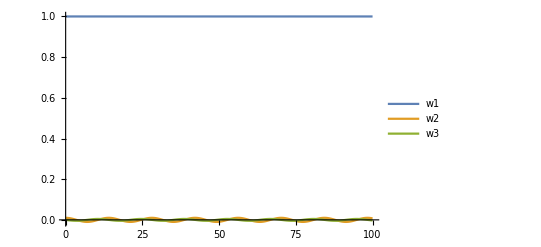

```mathematica
Plot[{w1[t]/.sol, w2[t]/.sol, w3[t]/.sol}, {t, 0, 100}, PlotLegends->{"w1", "w2", "w3"}]
```

### Rotation along second axis with perturbation along first axis

```mathematica
sol2=NDSolve[{w1'[t]==-w2[t]*w3[t], w2'[t]==w1[t]*w3[t], w3'[t]==-1/5 w2[t]*w1[t], w1[0]==0.01, w2[0]==1, w3[0]==0}, {w1[t], w2[t], w3[t]}, {t, 0, 100}];
```

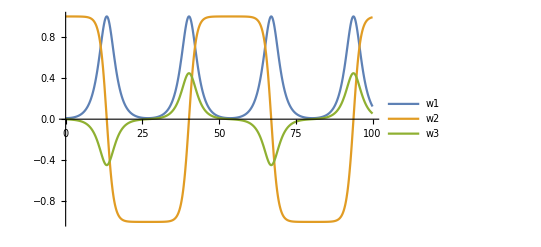

```mathematica
Plot[{w1[t]/.sol2, w2[t]/.sol2, w3[t]/.sol2}, {t, 0, 100}, PlotLegends->{"w1", "w2", "w3"}]
```

### Rotation along third axis with perturbation along second axis

```mathematica
sol3=NDSolve[{w1'[t]==-w2[t]*w3[t], w2'[t]==w1[t]*w3[t], w3'[t]==-1/5 w2[t]*w1[t], w1[0]==0, w2[0]==0.01, w3[0]==1},{w1[t], w2[t], w3[t]},{t, 0, 100}];
```

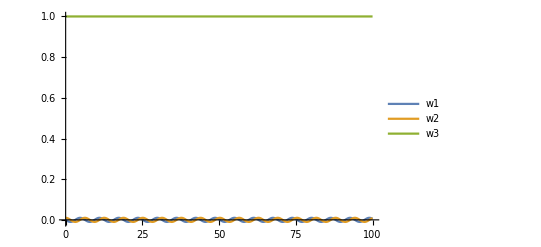

```mathematica
Plot[{w1[t]/.sol3, w2[t]/.sol3, w3[t]/.sol3}, {t, 0, 100}, PlotLegends->{"w1", "w2", "w3"}]
```

```mathematica
(*
Note: Mathematica could not solve the equations of motion analytically.
*)
```